```mathematica
(*(*
Thin disk model
N/Subscript[N, 0]=f(Subscript[ω, s])
(-4/5 πMR^2 P^2 Ṗ)/(2^(-1/14)Subscript[K, 0]^(1/2)(GM)^(3/7)u^(2/7)A^(-1/7)(Ṁ)^(6/7))=1-1/Subscript[ω, C]*2^(11/14)Subscript[πK, 0]^(3/2)(GM)^(-5/7)P^-1(Ṁ)^(-3/7)μ^(6/7)
*)
Clear[w,k,G,M,R,P,u,MEdd,a,b,x,A,Pdot1,Pdot2,Pdot3,Pdot4,equ,fig1]
w=0.7;
k=0.5;
G=6.67*10^-8;
M=2.8*10^33;
(*M=1.4 M_⊙*)
R=10^6;
P=1.37;
Pdot1=0.08;
Pdot2=-0.3;
Pdot3=-1.38;
Pdot4=-2.73;
(*q=Subscript[Ṗ, -10]={0.08,-0.3,-1.38,-2.73}*)
(*u=25;*)
(*μ=1/2 BR^3,B=5*10^13 G*)
MEdd=10^20;
a=1/w*k^(3/2)*(G*M)^(-5/7)*P^-1*(MEdd)^(-3/7)*2.80517*10^26;
(*a=1/Subscript[ω, C]*2^(11/14)Subscript[πK, 0]^(3/2)(GM)^(-5/7)P^-1 Subscript[Ṁ, E]^(-3/7)
=1/Subscript[ω, C]*2^(11/14)Subscript[πK, 0]^(3/2)(GM)^(-5/7)P^-1 Subscript[Ṁ, E]^(-3/7)Subscript[μ, 30]^(6/7)*(10^30)^(6/7)
2.^(11/14)*Pi*(10^30)^(6/7)=2.80517*10^26*)
b=(M*R^2*P^2)/(k^(1/2)*(G*M)^(3/7)*(MEdd)^(6/7))*(-7.08457*10^-19);
(*b=(-4/5 πMR^2 P^2)/(2^(-1/14)Subscript[K, 0]^(1/2)(GM)^(3/7)Subscript[Ṁ, E]^(6/7))
=(-4/5 πMR^2 P^2*10^-10)/(2^(-1/14)Subscript[K, 0]^(1/2)(GM)^(3/7)Subscript[Ṁ, E]^(6/7)*(10^30)^(2/7))
(-4/5*Pi*10^-10)/(2.^(-1/14)*(10^30)^(2/7))=-7.08457*10^-19*)
equ=x^(6/7)u^(2/7)-a*x^(3/7)u^(8/7)
b*Pdot1
b*Pdot2
b*Pdot3
b*Pdot4
(*
x=ṁ
Ṗ 和 ṁ 的关系
(b Subscript[Ṗ, -10])/(A^(-1/7)(ṁ)^(6/7)Subscript[μ, 30]^(2/7))=1-a(ṁ)^(-3/7)Subscript[μ, 30]^(6/7)
Subscript[Ṗ, -10]=(((ṁ)^(3/7)-a)(ṁ)^(3/7))/(b(1-ṁ)^(4/7)) (*A=(1-ṁ)^(1/2)*)
*)
ContourPlot[
{x^(6/7)*u^(2/7)-a*x^(3/7)*u^(8/7)-b*Pdot1==0,
x^(6/7)*u^(2/7)-a*x^(3/7)*u^(8/7)-b*Pdot2==0,
x^(6/7)*u^(2/7)-a*x^(3/7)*u^(8/7)-b*Pdot3==0,
x^(6/7)*u^(2/7)-a*x^(3/7)*u^(8/7)-b*Pdot4==0,
u-6==0,
u-26==0},
{x,0,1},{u,0.5,35},
PlotLabel->"Thin disk",
PlotLegends->{"(Ṗ)_-10=0.08","(Ṗ)_-10=-0.3","(Ṗ)_-10=-1.38","(Ṗ)_-10=-2.73"},FrameStyle->Thickness[0.001],FrameLabel->{"ṁ","μ_30"},
ContourStyle->{,,,,{Gray,Dotted},{Gray,Dotted}}]
(*(1-x)^(-1/14)x^(6/7)u^(2/7)-a(1-x)^(-4/7)x^(3/7)u^(8/7)-b*q==0,去掉b*q，即(1-x)^(-1/14)x^(6/7)u^(2/7)-a(1-x)^(-4/7)x^(3/7)u^(8/7)==b*q的康拓图
*)*)
```

-0.0476392 u^(8/7) x^(3/7)+u^(2/7) x^(6/7)

-0.0166932

0.0625994

0.287957

0.569654

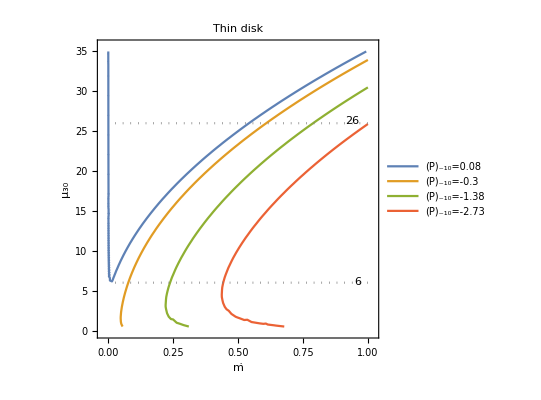

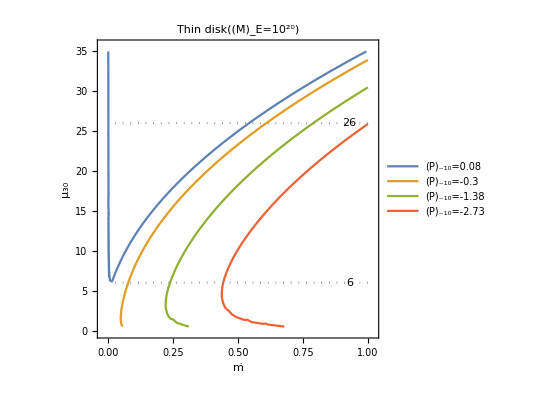

```mathematica
(*(*u=8*)
Clear[u,x]
u=10.0;
(*0.08*)FindRoot[equ==b*Pdot1,{x,0.9}]
(*-0.3*)FindRoot[equ==b*Pdot2,{x,0.9}]
(*-1.38*)FindRoot[equ==b*Pdot3,{x,0.9}]
(*-2.73*)FindRoot[equ==b*Pdot4,{x,0.9}]*)
```

{x→0.0677352}

{x→0.132135}

{x→0.29655}

{x→0.496902}

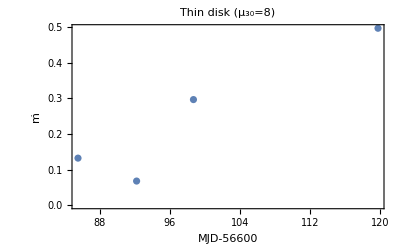

```mathematica
(*ListPlot[{{85.5,0.132135},{92.2,0.0677352},{98.7,0.29655},{119.8,0.496902}},FrameLabel->{"MJD-56600","ṁ"},Frame->True,PlotLabel->"Thin disk (μ_30=8)"]*)
```

```mathematica
(*不能解释观测*)
```